# Linear Regression

## CS229 Lecture Notes

## Introduction

To make our housing example more interesting, let’s consider a richer dataset.

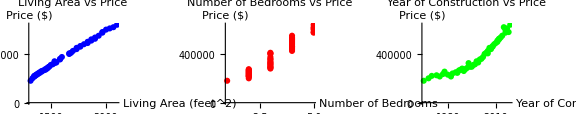

```mathematica
dataSet = {{1200,2,250000,1985},{1800,3,375000,2002},{2500,4,490000,2010},{1050,2,215000,1975},{3200,5,620000,2015},{1450,3,295000,1995},{2100,4,425000,2005},{950,1,180000,1965},{2700,4,525000,2012},{1600,3,340000,1998},{1350,2,270000,1988},{2300,4,465000,2008},{1100,2,230000,1980},{2900,5,580000,2018},{1750,3,355000,2000},{1250,2,260000,1990},{2600,4,510000,2011},{1500,3,310000,1996},{2000,3,400000,2003},{1050,2,220000,1970},{3000,5,600000,2016},{1400,3,285000,1992},{2200,4,440000,2007},{1150,2,240000,1983},{2800,4,550000,2014},{1650,3,330000,1999},{1300,2,265000,1987},{2400,4,480000,2009},{1000,2,200000,1968},{3100,5,610000,2017},{1550,3,315000,1997},{2050,3,410000,2004},{1250,2,255000,1978},{2700,4,535000,2013},{1350,2,275000,1991},{2200,4,450000,2006},{1100,2,225000,1973},{2500,4,500000,2011},{1450,3,295000,1994},{1750,3,360000,2001},{1050,2,215000,1982},{3300,5,640000,2019},{1600,3,325000,1993},{2300,4,460000,2008},{1200,2,245000,1986},{2600,4,520000,2012},{1400,3,280000,1989},{2000,3,405000,2005},{1150,2,235000,1977},{2900,5,575000,2016}};
(*Plot 1:Living Area (feet^2) vs Price*)plot1=ListPlot[Table[{dataSet[[i]][[1]],dataSet[[i]][[3]]},{i,1,Length[dataSet]}],PlotLabel->"Living Area vs Price",AxesLabel->{"Living Area (feet^2)","Price ($)"},PlotStyle->Blue,PlotMarkers->Automatic];

(*Plot 2:Number of Bedrooms vs Price*)
plot2=ListPlot[Table[{dataSet[[i]][[2]],dataSet[[i]][[3]]},{i,1,Length[dataSet]}],PlotLabel->"Number of Bedrooms vs Price",AxesLabel->{"Number of Bedrooms","Price ($)"},PlotStyle->Red,PlotMarkers->Automatic];

(*Plot 3:Year of Construction vs Price*)
plot3=ListPlot[Table[{dataSet[[i]][[4]],dataSet[[i]][[3]]},{i,1,Length[dataSet]}],PlotLabel->"Year of Construction vs Price",AxesLabel->{"Year of Construction","Price ($)"},PlotStyle->Green,PlotMarkers->Automatic];

(*Combine the plots*)
GraphicsGrid[{{plot1,plot2,plot3}},ImageSize->Large]
```

Here the  inputs would be a three dimensional vector in . Here’s the input or feature set:

```mathematica
inputSet = Table[{dataSet[[i]][[1]], dataSet[[i]][[2]], dataSet[[i]][[4]]},{i,1, Length[dataSet]}];
```

And the output or target set:

```mathematica
outputSet = Table[{dataSet[[i]][[3]]},{i,1,Length[dataSet]}]
```

{{250000},{375000},{490000},{215000},{620000},{295000},{425000},{180000},{525000},{340000},{270000},{465000},{230000},{580000},{355000},{260000},{510000},{310000},{400000},{220000},{600000},{285000},{440000},{240000},{550000},{330000},{265000},{480000},{200000},{610000},{315000},{410000},{255000},{535000},{275000},{450000},{225000},{500000},{295000},{360000},{215000},{640000},{325000},{460000},{245000},{520000},{280000},{405000},{235000},{575000}}

To preform supervised learning, we must decide how we’re going to represent functions/hypothesis  in a computer. As an initial choice, let’s say we decide to approximate  as a linear function of :

```mathematica
hypothesisFunction[x_,θ1_, θ2_, θ3_, θ4_]:= θ1 x[[1]] + θ2 x[[2]] + θ3 x[[3]] + θ4
```

where   are the parameters (also called weights) parameterizing the space of linear functions mapping from  to . We can gently provide a more general linear hypothesis function as:

or in Mathematica’s terms we define the module below.

```mathematica
linearHypothesisFunction[x_List]:= Function[theta, Sum[x[[i]] theta[[i]],{i,1,Length[x]}]+ theta[[Length[x]+1]]]
```

```mathematica
exampleH [theta_]:=linearHypothesisFunction[{1,2}][theta]
exampleH[{theta1,theta2,theta3}]
```

theta1+2 theta2+theta3

Below I presented the hypothesis for 1, 2, 3,

Keep in mind that we must define  to account for the constant term as well. Now given a training set, how do we pick, or learn, the parameters ? One reasonable method seems to be to make  close to , at least for the training examples we have. To formalize this, we will define a function that measures, for each value of the ’s, how close ’s are to the corresponding target. We therefore define the cost function:



If you’ve seen linear regression before, you may recognize this as the familiar least-squares cost function that gives rise to the ordinary least squares regression model. Whether or not you have seen it previously, let’s keep going and we’ll eventually show this to be a special case of a much broader family of algorithms.

```mathematica
costFunctionOfLinearHypothesisFunction[input_List, output_List]:=Function[theta,(1/2 Sum[(linearHypothesisFunction[input[[i]]][theta] - output[[i]])^2, {i, 1, Length[output]}]//Simplify)[[1]]]
```

```mathematica
J[θ_] := costFunctionOfLinearHypothesisFunction[inputSet, outputSet][θ]
```

## The Least Mean Square Algorithm

Now the problem is to minimize the cost function. To do so, let’s use a search algorithm that starts with some initial guess for , and repeatedly changes it to make the cost function smaller, until hopefully we converge to a value of  that minimizes . Specially, let’s consider the gradient descent algorithm, which starts with some initial , and repeatedly performs the update:

.
Here,  is called the learning rate. This is a very natural algorithm that repeatedly takes a step in the direction of steepest decrease of . In order to implement this algorithm, we have to work out what is the partial derivative term on the right hand side.

#### Example: Single training data, single step.

Let’s first work it out for the case of if we have only two training example, so that we can neglect the sum in the definition of .

```mathematica
exampleInput = {{4}};
exampleOutput= {{1}};
exampleCostFunction[theta_]:=costFunctionOfLinearHypothesisFunction[exampleInput, exampleOutput][theta]
exampleCostFunction[{t11,t22}]
```

1/2 (-1+4 t11+t22)^2

Let’s plot this to get a better view on the cost functions.

```mathematica
Plot3D[exampleCostFunction[{t1,t2}],{t1,-10,10},{t2,-10,10},PlotTheme->"Classic",AxesLabel->{"","","Cost"},Mesh->Full]
```

-Graphics3D-

For this single data, we first should have a guess value of .

```mathematica
initialGuess = {0,1};
α  =0.1;
t1 = initialGuess[[1]];
t2 = initialGuess[[2]];
{t1,t2}//MatrixForm
```

(0
1)

Now let’s do a single step of the update:

```mathematica
t1 = t1 - α D[exampleCostFunction[{t11,t2}],t11]//.t11->t1;
t2 = t2 - α D[exampleCostFunction[{t1,t22}],t22]//.t22->t2;
{t1,t2}//MatrixForm
ClearAll[t1,t2];
```

(0.
1.)

We don’t see any change and that’s because one training data is not sufficient for any kind of learning. But we’ll get back to it very quickly. 

Now let’s consider the derivative in the update formula of  components. if we wish to do this analytically, for the single training data (which is helpful and doesn’t contain complications), we can derive:
.
We can approve this derivation in Mathematica as well:

```mathematica
h[theta_]:=linearHypothesisFunction[exampleInput[[1]]][theta]
D[exampleCostFunction[{theta1,theta2}],theta1] == ((h[{theta1,theta2}] - exampleOutput[[1]]) exampleInput[[1]])[[1]]
```

True

Now let’s generalize this in various ways.

The rule is called the LMS update rule which stands for Least Mean Squares, and is also known as the Widrow-Hoff learning rule. This rule has several properties that seem natural and intuitive. For instance, the magnitude of the update is proportional to the error ; thus, for instance if we are encountering a training example on which our prediction nearly matches the actual value of , then we find that there is little need to change the parameters; in contrast, a larger change to the parameters will be made if our prediction has a large error.

We’d derive the LMS rule for when there was only a single training example. There are two ways to modify this method for a training set of more than one example.

#### Example: Multiple steps, and multiple training sets

In this example we first make the case for multiple training sets. The first step is to introduce data:

```mathematica
exampleMultipleInputs = Table[{i},{i,1,2}];
exampleMultipleOutputs = Table[{i},{i,1,2}];
```

Now let’s make things exciting by first introducing the cost function:

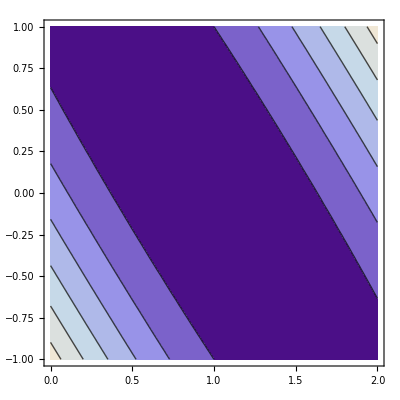

```mathematica
costFunction[theta_]:=costFunctionOfLinearHypothesisFunction[exampleMultipleInputs,exampleMultipleOutputs][theta]
plot=Plot3D[costFunction[{t1,t2}],{t1,0,2},{t2,1,-1},PlotTheme->"Classic",AxesLabel->{"","","Cost"},Boxed->True];
(*Generate the contour plot*)contourPlot=ContourPlot[costFunction[{t1,t2}],{t1,0,2},{t2,-1,1},ContourStyle->Opacity[0.7],PlotTheme->"Classic",AxesLabel->{"",""}];
GraphicsRow[{contourPlot, plot}]
```

Set::setraw: Cannot assign to raw object 1.

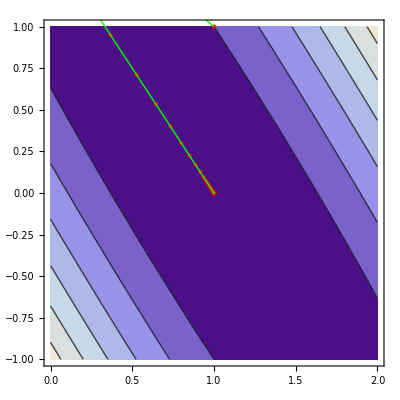

-Graphics3D-

```mathematica
ClearAll[numberOfSteps,initialGuess, α, t1,t2,points,path,stepPoints];
numberOfSteps=1000;
initialGuess={1,1};
α=1=0.5;
t1=initialGuess[[1]];
t2=initialGuess[[2]];
points={{t1,t2,costFunction[{t1,t2}]}};
path2D={{t1,t2}}; (*For 2D*)
For[i=1,i<numberOfSteps,i++,
t1=t1-α D[costFunction[{t11,t2}],t11]//.t11->t1;
t2=t2-α D[costFunction[{t1,t22}],t22]//.t22->t2;
AppendTo[points,{t1,t2,costFunction[{t1,t2}]}];
AppendTo[path2D,{t1,t2}];
];

path=Graphics3D[{Thin,Pink,Line[points]}];
stepPoints=Graphics3D[{Purple,PointSize[Large],Point[points]}];

(*Add 2D path and points*)
path2DPlot=Graphics[{Thick,Green,Line[path2D]}];
stepPoints2D=Graphics[{Red,PointSize[Large],Point[path2D]}];

Show[{contourPlot,stepPoints2D, path2DPlot}]
Show[{plot, path, stepPoints}]
```